```mathematica
SetDirectory[NotebookDirectory[]];
Needs["PlotLegends`"]
```

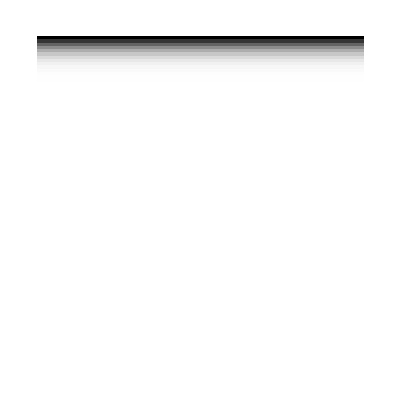

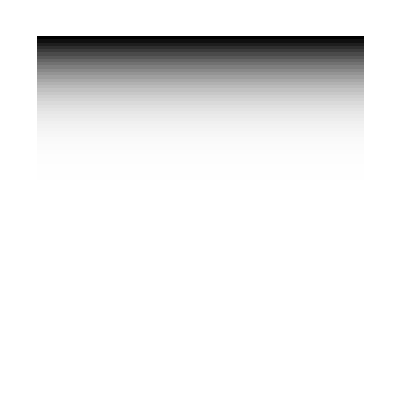

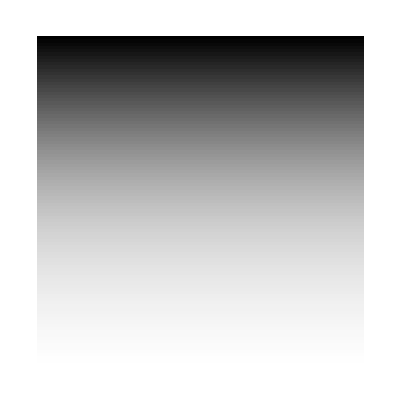

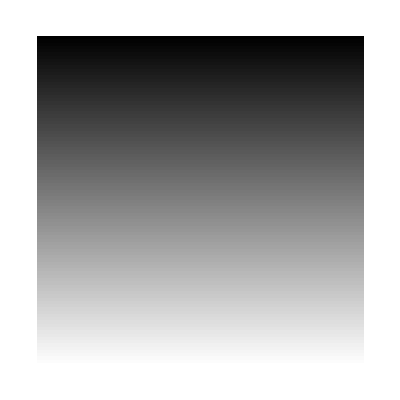

```mathematica
ArrayPlot[Import["data.i0p0","Table"]];
ArrayPlot[Import["data.i100p0","Table"]]
ArrayPlot[Import["data.i1000p0","Table"]]
ArrayPlot[Import["data.i10000p0","Table"]]
ArrayPlot[Import["data.i100000p0","Table"]]
```

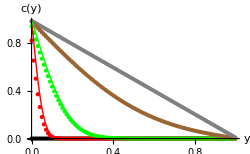

```mathematica
b=Show[ListPlot[{Flatten[Drop[Import["data.i0p0","Table"],None,-99]],Flatten[Drop[Import["data.i100p0","Table"],None,-99]],Flatten[Drop[Import["data.i1000p0","Table"],None,-99]],Flatten[Drop[Import["data.i10000p0","Table"],None,-99]],Flatten[Drop[Import["data.i100000p0","Table"],None,-99]]},DataRange->{0,1},PlotStyle->{Black,Red,Green,Brown,Gray}],ListPlot[{Flatten[Drop[Reverse[Import["t0001.txt","Table"]],None,1]],Flatten[Drop[Reverse[Import["t001.txt","Table"]],None,1]],Flatten[Drop[Reverse[Import["t01.txt","Table"]],None,1]],Flatten[Drop[Reverse[Import["t1.txt","Table"]],None,1]]},Joined->True,PlotStyle->{Red,Green,Brown,Gray},DataRange->{0,1}],AxesLabel->{"y","c(y)"},ImageSize->250]
```